```mathematica
(* Voreen transfer function *)
tf=Import["D:\\document\\work\\artivvis-development-repository\\data\\Tooth\\tooth.tfi","XML"];
intensity=ToExpression@Cases[tf,XMLElement["intensity",{"value"->atrib_,___},___]:>atrib,∞];
r=ToExpression@Cases[tf,XMLElement["colorL",{"r"->atrib_,___},___]:>atrib,∞];
g=ToExpression@Cases[tf,XMLElement["colorL",{___,"g"->atrib_,___},___]:>atrib,∞];
b=ToExpression@Cases[tf,XMLElement["colorL",{___,"b"->atrib_,___},___]:>atrib,∞];
a=ToExpression@Cases[tf,XMLElement["colorL",{___,"a"->atrib_},___]:>atrib,∞];
rgb=(#/255.&)/@Transpose[{r,g,b}]//(RGBColor/@#&);
rgbfunction=(Blend[Transpose[{intensity,rgb}], #1] & );
rgba=(#/255.&)/@Transpose[{r,g,b,a}]//(RGBColor/@#&);
rgbafunction=(Blend[Transpose[{intensity,rgba}], #1] & );
alpha=(#/255.&)/@a;
bincount=256;
{rgb,rgba}
```

{{RGBColor[{0., 0.6666666666666666, 1.}],RGBColor[{0., 0.6666666666666666, 1.}],RGBColor[{0., 0.6666666666666666, 1.}],RGBColor[{1., 0., 0.}],RGBColor[{1., 0., 0.}],RGBColor[{1., 0., 0.}],RGBColor[{1., 1., 0.}],RGBColor[{1., 1., 0.}],RGBColor[{1., 1., 0.}]},{RGBColor[{0., 0.6666666666666666, 1., 0.}],RGBColor[{0., 0.6666666666666666, 1., 0.27450980392156865}],RGBColor[{0., 0.6666666666666666, 1., 0.}],RGBColor[{1., 0., 0., 0.}],RGBColor[{1., 0., 0., 0.27450980392156865}],RGBColor[{1., 0., 0., 0.}],RGBColor[{1., 1., 0., 0.}],RGBColor[{1., 1., 0., 0.27450980392156865}],RGBColor[{1., 1., 0., 0.}]}}

```mathematica
(* Slicer transfer function *)
tf=Import["D:\\document\\work\\artivvis-development-repository\\transferfuncs\\presets.xml"];
tfname="CT-AAA";
intensitylist=ToExpression@StringSplit@First@Cases[tf,XMLElement["VolumeProperty",{___,"name"->tfname,___,"scalarOpacity"->atrib_,___},___]:>atrib,∞]//Partition[#[[2;;All]],2]&//Transpose;
irgblist=ToExpression@StringSplit@First@Cases[tf,XMLElement["VolumeProperty",{___,"name"->tfname,___,"colorTransfer"->atrib_,___},___]:>atrib,∞]//Partition[#[[2;;All]],4]&//Transpose;
intensity=First[intensitylist];
If[intensity[[1]]<0,intensity[[1]]=0];
intensity=Rescale[intensity];
r=irgblist[[2]];
g=irgblist[[3]];
b=irgblist[[4]];
a=Last[intensitylist];
rgb=RGBColor/@Transpose[{r,g,b}];
rgba=RGBColor/@Transpose[{r,g,b,a}];
rgbfunction=(Blend[Transpose[{intensity,rgb}], #1] & );
rgbafunction=(Blend[Transpose[{intensity,rgba}], #1] & );
{rgb,rgba}
```

{{RGBColor[{0, 0, 0}],RGBColor[{0.615686, 0.356863, 0.184314}],RGBColor[{0.882353, 0.603922, 0.290196}],RGBColor[{1, 1, 1}],RGBColor[{1, 0.937033, 0.954531}],RGBColor[{0.827451, 0.658824, 1}]},{RGBColor[{0, 0, 0, 0}],RGBColor[{0.615686, 0.356863, 0.184314, 0}],RGBColor[{0.882353, 0.603922, 0.290196, 0.686275}],RGBColor[{1, 1, 1, 0.696078}],RGBColor[{1, 0.937033, 0.954531, 0.833333}],RGBColor[{0.827451, 0.658824, 1, 0.803922}]}}

```mathematica
knee=ExampleData[{"TestImage3D","MRknee"}];
segm1=ClusteringComponents[MedianFilter[knee,1],3];
Image3D[Colorize[segm1],ClipPlanes->{{-1,1,0,12}}];
label=SortBy[ComponentMeasurements[{knee,segm1},"MeanIntensity"],Last][[-1,1]];
boneFat=Image3D[SelectComponents[segm1,"Label",#==label&]];
boneCore=Dilation[DeleteSmallComponents@Erosion[boneFat,4],1];
boneShell=MorphologicalPerimeter[Dilation[boneCore,6],Padding->1];
segm2=MedianFilter[Image3D[2-GrowCutComponents[knee,{boneCore,boneShell}]],1];
ImageMultiply[knee,Blur[segm2,2]];
components=MorphologicalComponents[segm2];
ComponentMeasurements[{components,knee},{"Shape","FilledCount","Mean","StandardDeviation"}]
```

{1→{-Graphics3D-,52895,0.681652,0.106183},2→{-Graphics3D-,30700,0.637169,0.0734151}}

```mathematica
f1=Clip[components/.{2->0},{0,1}]//Image3D;
f2=Clip[components/.{1->0},{0,1}]//Image3D;
features={f1,f2}
```

{-Graphics3D-,-Graphics3D-}

-Graphics3D-

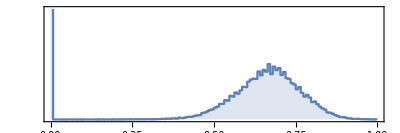

```mathematica
bone=ImageMultiply[knee,segm2]
ImageHistogram[bone]
```

```mathematica
r=ImageApply[List@@rgbafunction[#]&,bone]//Image3D[#,ColorSpace->"RGB"]&
```

-Graphics3D-

-Graphics-

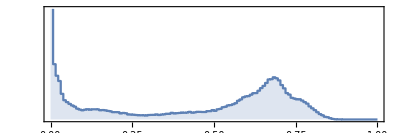

```mathematica
bone//ImageHistogram
GaussianFilter[bone,2]//ImageHistogram
```

```mathematica
mhd=StringTemplate["NDims = 3
DimSize = `` `` ``
ElementType = MET_UCHAR
ElementSpacing = 1.0 1.0 1.0
ElementByteOrderMSB = False
ElementDataFile = ``
"];
dat="ObjectFileName: ``
TaggedFileName: ---
Resolution:     `` `` ``
SliceThickness: 1.0 1.0 1.0
Format:         UCHAR
NbrTags:        0
ObjectType:     TEXTURE_VOLUME_OBJECT
ObjectModel:    RGBA
GridType:       EQUIDISTANT
Modality:       unknown
TimeStep:       0
Unit:           mm
";
```

```mathematica
Export[NotebookDirectory[]<>"MRknee_RGBA.raw",Flatten@ImageData[r,"Byte"],{"Binary","Byte"}];
Export[NotebookDirectory[]<>"MRknee_RGBA.mhd",TemplateApply[mhd,Join[ImageDimensions[r],{"MRknee_RGBA.raw"}]],"Text"];
Export[NotebookDirectory[]<>"MRknee_RGBA.dat",TemplateApply[dat,Join[{"MRknee_RGBA.raw"},ImageDimensions[r]]],"Text"];
```

```mathematica
Export[NotebookDirectory[]<>"MRknee_bone.raw",Flatten@ImageData[bone,"Byte"],{"Binary","Byte"}];
Export[NotebookDirectory[]<>"MRknee_bone.mhd",TemplateApply[mhd,Join[ImageDimensions[bone],{"MRknee_bone.raw"}]],"Text"];
```

```mathematica
(* export in little-endian (byte ordering on current computer) *)
Export[NotebookDirectory[]<>"MRknee_little-endian.raw",Flatten@ImageData[knee,"Bit16"],{"Binary","UnsignedInteger16"}];
```

```mathematica
cl=ClusteringComponents[MedianFilter[knee,1],3,Method->"KMeans",DistanceFunction->EuclideanDistance];
f1=Clip[cl/.{2->0,3->0},{0,1}]//Image3D;
f2=Clip[cl/.{1->0,3->0},{0,1}]//Image3D;
f3=Clip[cl/.{1->0,2->0},{0,1}]//Image3D;
f={f1,f2,f3}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
Export[NotebookDirectory[]<>"MRknee_feature1.raw",Flatten@ImageData[ImageMultiply[knee,f1],"Byte"],{"Binary","Byte"}];
Export[NotebookDirectory[]<>"MRknee_feature2.raw",Flatten@ImageData[ImageMultiply[knee,f2],"Byte"],{"Binary","Byte"}];
Export[NotebookDirectory[]<>"MRknee_feature3.raw",Flatten@ImageData[ImageMultiply[knee,f3],"Byte"],{"Binary","Byte"}];
```